```mathematica
-
```

# Quadratic Soma Neuron Model

## Preface

Everything in the preface is meant to be general code that should be applicable to any notebook.In most cases,this section will house commands/scripts that add functionality to the notebook,regardless of the content of the notebook

## Input cell folding

The following code is a script that adds a button to turn all input cells off,thereby just showing the plots,outputs,and/or manipulators.

```mathematica
ShowInputCells[sh_]:=SetOptions[#,CellOpen->sh]&/@Cells[EvaluationNotebook[],CellStyle->{"Input"}]

SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[DynamicModuleBox[{showHide$$=True},TemplateBox[{"\"Show/hide input cells \"",CheckboxBox[Dynamic[showHide$$,{(showHide$$=#)&,ShowInputCells[showHide$$]&}]]},"RowDefault"],DynamicModuleValues:>{}]],"Output"]]
```

## Workspace

## Function Definitions

### Conversion functions from dimensionless forms to dimensional currents

```mathematica
iIntoIin[iIn_,Ilk_,pqua_,pilkr_]:=(iIn (Ilk+pilkr)^2)/(pqua Ilk)
iIntoIlkP[iIn_,Iin_,pqua_,pilkr_]:=(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
iIntoIlkN[iIn_,Iin_,pqua_,pilkr_]:=(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
tauToIlk[tau_,ptau_,pilkr_]:=ptau/tau-pilkr
trefToIref[tref_,pref_]:=pref/tref
trToIref[tr_,Iin_,Ilk_,pref1_,pref2_]:=(pref1-pref2 Log[Iin Ilk])/tr
```

#### Derivation of the relation between i_in and I_in or I_lk

Solve for I_in or I_lk in terms of i_in, I_lk/I_in (respectively), ρ_qua, and ρ_ilkr.  These solve equations were used to get the values for iIntoIlkP and iIntoIlkN above.

```mathematica
Solve[pqua ((Iin Ilk)/(Ilk+pilkr)^2)==iIn,Iin]
Solve[pqua ((Iin Ilk)/(Ilk+pilkr)^2)==iIn,Ilk]
```

{{Iin→(iIn (Ilk+pilkr)^2)/(Ilk pqua)}}

{{Ilk→(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)},{Ilk→(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)}}

#### Test Plot showing I_in to I_lk relation for a given value of i_in

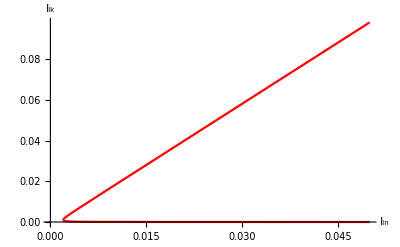

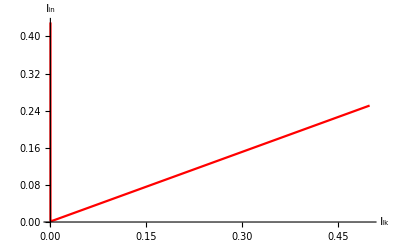

```mathematica
tmpiIn=1.0;
Plot[{iIntoIlkP[tmpiIn,Iin,pquatmp,pilkrtmp],iIntoIlkN[tmpiIn,Iin,pquatmp,pilkrtmp]},{Iin,0,0.05},PlotStyle->Red,AxesLabel->{"I_in","I_lk"}]
Plot[{iIntoIin[tmpiIn,Ilk,pquatmp,pilkrtmp]},{Ilk,0,0.5},PlotStyle->Red,AxesLabel->{"I_lk","I_in"}]
```

### i_in function

iIn is also the equivalent of defining i_in as a function of dimensional units (I_in, I_lk, ρ_qua, and  ρ_ilkr)

```mathematica
iIn[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
```

### τ function

```mathematica
τ[Ilk_,ptau_,pilkr_]:=ptau/(Ilk+pilkr)
```

### t_ref functions

t_ref is assumed to be a close approximation for the actual amount of time that the neuron stays in refraction.  This is based on the fact that C_r was assumed to charge up to V_dd.  In contrast, t_r is the actual amount of time that the neuron stays in refraction, based on when C_r charges up to a specific V_r corresponding to the point where I_lk+I_lr=I_b+I_fb.  At this point, we can assume that V_m, the membrane voltage, starts to decrease again, and the soma starts its firing process.  The derivation for t_r can be found in the notebook titled “RefractoryPeriodModel.nb”.

```mathematica
tref[Iref_,pref_]:=pref/Iref
tr[Iin_,Ilk_,Iref_,pref1_,pref2_]:=(pref1-pref2 Log[Iin Ilk])/Iref
```

### h(i_in) Functions

```mathematica
h[iIn_,β0_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]-ArcTan[(β0-1)/(√(2 iIn-1))]))/(√(2 iIn-1))
hβ0[iIn_,β0_]:=(π-2ArcTan[(β0-1)/(√(2 iIn-1))])/(√(2 iIn-1))
hβf[iIn_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]+ArcCot[√(2 iIn-1)]))/(√(2 iIn-1))
h[iIn_]:=(π+2ArcCot[√(2 iIn-1)])/(√(2 iIn-1))
```

### Dynamical systems equation of QIF neuron

```mathematica
imDot[im_,iin_,τ_]:=(1/2 im^2-im + iin)/τ
imDot[im_,Iin_,Ilk_,pqua_,ptau_,pilkr_] :=(1/2 im^2-im + iIn[Iin,Ilk,pqua,pilkr])/τ[Ilk,ptau,pilkr]
```

### Firing rate functions

#### Without refractory period, f_0

f_0=1/(τ·h(i_in)); τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2

```mathematica
f0[iIn_,τ_]=1/(τ h[iIn]);
f0[iIn_,β0_,βf_,τ_]=1/(τ h[iIn,β0,βf]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_,plkb_]=1/(τ[Ilk,ptau,pilkr,plkb] h[iIn[Iin,Ilk,pqua,pilkr,plkb]]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_,plkb_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr,plkb] h[iIn[Iin,Ilk,pqua,pilkr,plkb],β0,βf]);
```

#### With refractory period, f

f=1/(τ·h(i_in)+t_ref)τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2, t_ref=ρ_ref/I_ref

```mathematica
f[iIn_,τ_,tref_]=1/(τ h[iIn]+tref);
f[iIn_,β0_,βf_,τ_,tref_]=1/(τ h[iIn,β0,βf]+tref);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]+tref[Iref,pref]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]+tref[Iref,pref]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref1_,pref2_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr]]+tr[Iin,Ilk,Iref,pref1,pref2]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref1_,pref2_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[iIn[Iin,Ilk,pqua,pilkr],β0,βf]+tr[Iin,Ilk,Iref,pref1,pref2]);
```

## Dimensionless bifurcation model and quadratic firing rate model

```mathematica
DynamicModule[{iin=.51,tau=.015,tauref=0.001,imMax=5, idotMin = 0,idotMax=20, iInMax=2,fMax = 40, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["i_in",labelSize],Slider[Dynamic[iin],{0.01,2}],InputField[Dynamic[iin],FieldSize->5]},
{Style["τ_m",labelSize],Slider[Dynamic[tau],{0.001,.050,0.001}],InputField[Dynamic[tau],FieldSize->5]},{Style["t_ref",labelSize],Slider[Dynamic[tauref],{0.001,0.02,0.001}],InputField[Dynamic[tauref],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[iin],Background->LightGray]},
{Style["τ_m",labelSize],Panel[Dynamic[tau],Background->LightGray]},
{Style["t_ref",labelSize],Panel[Dynamic[tauref],Background->LightGray]}},
Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{imDot[imem,iin,tau]},{imem,0,imMax},PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,iIn≤0},{f[iIn,tau,tauref],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,tau,0],iIn>0.5}}],
f[iin,tau,tauref],
f[iin,tau,0]},
{iIn,0,iInMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{iin,f[iin,tau,0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iin,f[iin,tau,tauref]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[iin,tau, 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[iin,tau, 0]-f[iin,tau, tauref]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["v_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(v̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(v̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["v_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(v_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->14,titleLabelSize->12,ImgSize->400}
```

## Dual-bias dimensional bifurcation model and quadratic firing rate model

### Dependent ρ_val parameters

```mathematica
DynamicModule[{Iin=.2,Ilk=.595,Iref=7.333,pqua=1.44439,ptau=0.00100,pilkr=0.00682,pref=0.022,pref1=-3.01409,pref2=0.83683,imMax=5, idotMin = 0,idotMax=200, iInMax=2,fMax = 175, ilitMax=3,Cmin=0.000035465, Cmax=3131.22},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_in",labelSize],Slider[Dynamic[Iin],{0.01,5}],InputField[Dynamic[Iin],FieldSize->5]},{Style["I_lk",labelSize],Slider[Dynamic[Ilk],{0.01,1,0.005}],InputField[Dynamic[Ilk],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,10}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},
{Style["ρ_ilkr",labelSize],Slider[Dynamic[pilkr],{0.0001,0.005}],InputField[Dynamic[pilkr],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}
},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_ref1",labelSize],Slider[Dynamic[pref1],{-10.,0.2,0.01}],InputField[Dynamic[pref1],FieldSize->5]},
{Style["ρ_ref2",labelSize],Slider[Dynamic[pref2],{0,3.0,0.01}],InputField[Dynamic[pref2],FieldSize->5]}
},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["i_in",labelSize],Panel[Dynamic[iIn[Iin,Ilk,pqua,pilkr]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τ[Ilk,ptau,pilkr]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[tref[Iref,pref]],Background->LightGray]},
{Style["t_r",labelSize],Panel[Dynamic[tr[Iin,Ilk,Iref,pref1,pref2]],Background->LightGray]}
},Alignment->{Left,Left},Spacings->{1,0}]

}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{imDot[imem,Iin,Ilk,pqua,ptau,pilkr]},{imem,0,imMax},
PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["i_m",labelSize],Style["OverDot[i_m]",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],tref[Iref,pref]],curiIn>0.5}}],
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],0],curiIn>0.5}}],
Piecewise[{{None,curiIn≤0.5},{f[curiIn,τ[Ilk,ptau,pilkr],tr[iIntoIin[curiIn,Ilk,pqua,pilkr],Ilk,Iref,pref1,pref2]],curiIn>0.5}}],
Piecewise[{
{None,curiIn≤0.5},
{f[curiIn,τ[Ilk,ptau,pilkr],tr[iIntoIin[curiIn,tauToIlk[τ[Ilk,ptau,pilkr],ptau,pilkr],pqua,pilkr],tauToIlk[τ[Ilk,ptau,pilkr],ptau,pilkr],Clip[Iref,{Cmin,Cmax}],pref1,pref2]],curiIn>0.5}
}]
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tref[Iref,pref]],
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],0],
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]
},{curiIn,0,iInMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {Blue, Darker[Red],Orange,{Dashed,Blue},{Dashed,Darker[Red]},{Dashed,Orange}},AxesLabel->{Style["i_in",labelSize],Style["f(i_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua,pilkr],f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,iIn≤0},{f[iIn,τ[Ilk,ptau,pilkr],tref[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τ[Ilk,ptau,pilkr],0],iIn>0.5}}]*)
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],tref[Iref,pref]],
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],0],
f[iIn[Iin,Ilit,pqua,pilkr],τ[Ilit,ptau,pilkr],tr[Iin,Ilk,Iref,pref1,pref2]]
},{Ilit,0,ilitMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {Darker[Red],Blue,Orange},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{iIn[Iin,Ilk,pqua],f[iIn[Iin,Ilk,pqua],τ[Ilk,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iIn[Iin,Ilk,pqua],f[iIn[Iin,Ilk,pqua],τ[Ilk,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]],Background->LightGray]},
{Style["f_t_ref",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tref[Iref, pref]]],Background->LightGray]},
{Style["f_t_r",labelSize],Panel[Dynamic[f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tr[Iin,Ilk,Iref, pref1,pref2]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]-f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tref[Iref, pref]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[
f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], 0]-f[iIn[Iin,Ilk,pqua,pilkr],τ[Ilk, ptau,pilkr], tr[Iin, Ilk,Iref, pref1,pref2]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["i_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(i̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(i̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["i_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(i_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->12,titleLabelSize->11,ImgSize->350}
```

## h(i_in) vs i_in plot

```mathematica
Series[h[iIn],{iIn,.5,0}]
```

(√2 π)/(√(vin-0.5))-2+O((vin-0.5)^1)

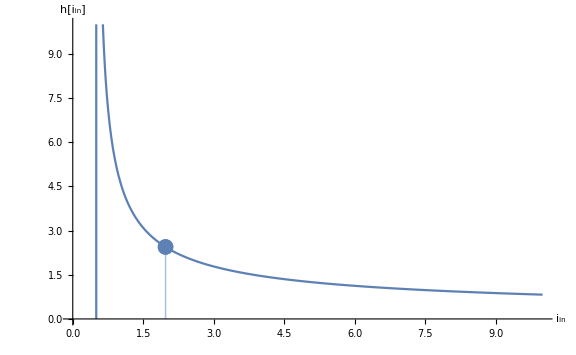

```mathematica
Show[
Plot[h[iIn],{iIn,0,10},
ImageSize->Large,
AxesLabel->{"i_in","h[i_in]"},
PlotRange-> {0,10}],
ListPlot[{{1.97481,h[1.97481]}},Filling->Axis]
]
```

```mathematica
h[.8]
```

6.40988

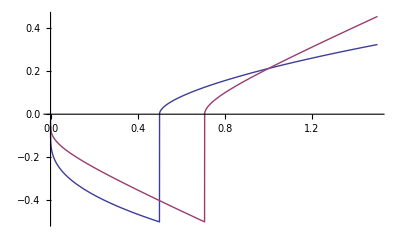

```mathematica
Plot[{h[iIn]^-1,h[(iIn)^2]^-1},{iIn,0,1.5}]
```

Find out at what point the h[i_in] function starts to explode (defined as when the slope is smaller than -1)

```mathematica
h[iin]
h'[iin]
dh[iin]=-(1/(iin (2 iin-1)))-(2 ArcCot[Sqrt[2 iin-1]]+π)/(2 iin-1)^(3/2)
```

(2 cot^-1(√(2 iIn-1))+π)/(√(2 iIn-1))

-1/(iIn (2 iIn-1))-(2 cot^-1(√(2 iIn-1))+π)/(2 iIn-1)^(3/2)

-1/(iIn (2 iIn-1))-(2 cot^-1(√(2 iIn-1))+π)/(2 iIn-1)^(3/2)

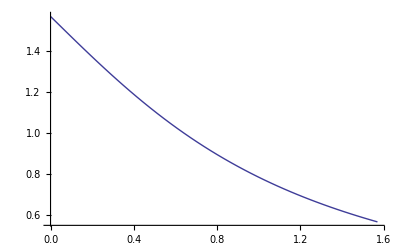

```mathematica
Plot[ArcCot[b],{b,0,π/2}]
```

```mathematica
FindRoot[dh[iin]==-1,{iin,1.5}]
```

{vin→1.97481}

```mathematica
h[{1.7,1.6, 0.6}]/0.03
```

{92.2631,97.2644,405.631}

```mathematica
Limit[h'[iin],iin->∞]
```

0

```mathematica
Limit[1/h[iin],iin->∞]
```

∞

```mathematica
Limit[1/dh[iin],iin->0.5]
```

0.

```mathematica
D[h[iin]^-2, iin]/.iin->{0.5,0.51,0.52}
```

{0.0506606,0.0580795,0.0614491}

## Appendix/Workspace

### Solve for Voltage Membrane

This section doesn’t work.  It has been moved to the appendix until it works or makes more sense.

```mathematica
solution=DSolve[{im'[t]τ==1/2(im[t])^2-im[t]+iIn[Iin,Ilk,pqua,pilkr], im[0]==1},im[t],t]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{im(t)→(tan((t Ilk^3)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pqua t Ilk^2)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr t Ilk^2)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pilkr pqua t Ilk)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr^2 t Ilk)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(pilkr^3 t)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)) Ilk^2+2 pilkr tan((t Ilk^3)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pqua t Ilk^2)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr t Ilk^2)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pilkr pqua t Ilk)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr^2 t Ilk)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(pilkr^3 t)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)) Ilk-2 Iin pqua tan((t Ilk^3)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pqua t Ilk^2)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr t Ilk^2)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pilkr pqua t Ilk)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr^2 t Ilk)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(pilkr^3 t)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)) Ilk+√(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) Ilk+pilkr^2 tan((t Ilk^3)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pqua t Ilk^2)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr t Ilk^2)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)-(Iin pilkr pqua t Ilk)/((Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(3 pilkr^2 t Ilk)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ)+(pilkr^3 t)/(2 (Ilk+pilkr)^2 √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2) τ))+pilkr √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2))/((Ilk+pilkr) √(-Ilk^2-2 pilkr Ilk+2 Iin pqua Ilk-pilkr^2))}}

```mathematica
SetOptions[Plot, PlotPoints->400];
Manipulate[
solution=DSolve[{im'[t]τ==1/2(im[t])^2-im[t]+VinStackedBias[Iin,Ilk,pqua,pilkr], im[0]==1},im[t],t][[1]];
Plot[im[t]/.solution,{t,0,10}],
{{τ,.01},0,1,.05,Appearance->"Labeled"},
{{Iin,.1},0.01,.3,.01,Appearance->"Labeled"},
{{Ilk,.1},0.01,.2,.005,Appearance->"Labeled"},
{{pqua,.51},0.5,6,.25,Appearance->"Labeled"},
{{pilkr,0.00051},0.00005,0.005,.00005,Appearance->"Labeled"},
TrackedSymbols:>{τ,Iin,Ilk,pqua,pilkr}
]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

### Investigation into discontinuous model fits during calibration

While calibrating Chip 3 of endeavour, I found that using the firing rate including t_ref calibration model, the output theoretical curves had some discontinuities for large I_lk and large I_in, when i_in is still relatively small.  In other words, when the firing rate was small, for some of the larger I_in and I_lk values, we saw that the curve breaks shape and has a steeper, linear looking slope.  I wanted to model this in Mathematica to see if it’s a real effect caused by the t_ref compensation term or if it’s something that python is interpolating incorrectly for some reason.

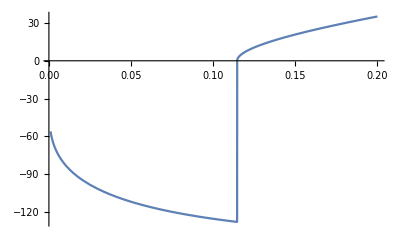

```mathematica
Plot[f[Iin,Ilk,Iref,pqua,ptau,pilkr,pref1,pref2]/.{Ilk->0.182,Iref->1000,pqua->0.86327991, ptau->0.00093283,pilkr->0.00774582,pref1->-6.46045381,pref2->2.18765869},{Iin,0.001,.20}]
```

### Investigation into effects on FI curve if current is bounded by C_max or C_min

```mathematica
Manipulate[
Grid[{
{
Plot[{
Piecewise[{
{None,curiIn≤0.5},
{f[curiIn,tau,0],curiIn>0.5}
}],
(*ADD CODE that converts tref to an Iref value and caps it if it exceeds Subscript[C, max] or is below Subscript[C, min]*)
Piecewise[{
{None,curiIn≤0.5},
{f[curiIn,tau,tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2]],curiIn>0.5}
}]
},{curiIn,0,iInMax},
AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],
PlotStyle-> {{Darker[Red],Dashed},Orange},AxesLabel->{Style["i_in",labelSize],Style["f(i_in)",labelSize]},ImageSize->ImgSize]
,
Plot[{
tref1,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
(*tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmin,pref1,pref2]*)(*,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmax,pref1,pref2]*)
},{curiIn,0,3},
ImageSize->ImgSize,PlotRange->{-.0001,3*tref1},PlotStyle->{Dashed,Solid},AxesLabel->{"i_in","t_r"},
Epilog->Inset[
Plot[
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
{curiIn,0,3},
PlotRange->{-0.001,0.001},ImageSize->ImgSize/2],
{2.5,0.0002}
]
],
Plot[
pref1-pref2 Log[iIntoIin[curiIn, tauToIlk[tau,ptau,pilkr],pqua,pilkr] tauToIlk[tau,ptau,pilkr]],
{curiIn,0,3},
ImageSize->ImgSize,PlotRange->{-5,5},AxesLabel->{"i_in","p_ref1-p_ref2*log(I_inI_lk)"}
]
},{
Grid[
{
{
tref1,
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}],pref1,pref2],
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmin,pref1,pref2],
tr[iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],Cmax,pref1,pref2]
},
{
trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],
Clip[trToIref[tref1,iIntoIin[curiIn,tauToIlk[tau,ptau,pilkr],pqua,pilkr],tauToIlk[tau,ptau,pilkr],pref1,pref2],{Cmin,Cmax}]
}
}]
}}
]
,
{{curiIn,1.15},0,3,0.001, Appearance->"Open"},
{{iInMax,2},1,5,0.01},
{{fMax,100},50,500,1}
]/.{tau->0.010,tref1->0.0001,pqua->0.745379,ptau->0.00103434,pilkr->0.00574933,pref1->0.043937,pref2->0.00097134,Cmin->0.000035465, Cmax->3131.22,labelSize->12,titleLabelSize->11,ImgSize->350}
```

## Play Section

```mathematica
tr[0.194914,0.232714,13.997,-0.06314637,0.36832799,18.50241418]
```

0.0000999981

## Old/Obsolete

## Stacked Bias formulation

τ_m i_m^•= -v_m+v_m^2/2+ v_in
i_in=ρ_qua(I_c^2/I_l^2)

```mathematica
VmdotTheory[Vm_,iin_,τ_]:=(1/2 Vm^2-Vm + iin)/τ
VmdotStackedBias[Vm_,Ic_,Il_,τ_,pqua_] :=(1/2 Vm^2-Vm + VinStackedBias[Ic,Il,pqua])/τ
VinStackedBias[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
τOBS[Il_,ptau_]:=ptau/Il
trefOBS[Iref_,pref_]:=pref/Iref
```

This method of calculating the biases is the method that was used in Peiran’s paper where I_bk was created using two transistors stacked on each other such that you would get I_bk^2.  This method isn’t as clean/interesting as the new method which automatically scales I_in with I_lk.

```mathematica
DynamicModule[{Ic=.5,Il=.595,Iref=7.333,pqua=1.50316,ptau=0.00119,pref=0.022, imMax=5, idotMin = 0,idotMax=20, iInMax=2,fMax = 175, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_c",labelSize],Slider[Dynamic[Ic],{0.01,5}],InputField[Dynamic[Ic],FieldSize->5]},{Style["I_l",labelSize],Slider[Dynamic[Il],{0.01,1,0.005}],InputField[Dynamic[Il],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,10}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[VinStackedBias[Ic,Il,pqua]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τOBS[Il,ptau]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[trefOBS[Iref,pref]],Background->LightGray]}},Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{VmdotStackedBias[Vmem,Ic,Il,τOBS[Il,ptau],pqua]},{Vmem,0,imMax},PlotRange->{idotMin,idotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],trefOBS[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],0],iIn>0.5}}],
f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]],
f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]},
{iIn,0,iInMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],trefOBS[Iref,pref]],iIn>0.5}}],
Piecewise[{{0,iIn≤0},{f[iIn,τOBS[Il,ptau],0],iIn>0.5}}]*)
f[VinStackedBias[Ic,Ilit,pqua],τOBS[Ilit,ptau],trefOBS[Iref,pref]],
f[VinStackedBias[Ic,Ilit,pqua],τOBS[Ilit,ptau],0]},
{Ilit,0,ilitMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Darker[Red],Blue},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τOBS[Il,ptau],trefOBS[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], 0]-f[VinStackedBias[Ic,Il,pqua],τOBS[Il, ptau], trefOBS[Iref, pref]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["i_m_max",labelSize],Slider[Dynamic[imMax],{0.,20}],InputField[Dynamic[imMax],FieldSize->5]},
{Style["(i̇)_min",labelSize],Slider[Dynamic[idotMin],{-10,0}],InputField[Dynamic[idotMin],FieldSize->5]},{Style["(i̇)_max",labelSize],Slider[Dynamic[idotMax],{10,200}],InputField[Dynamic[idotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["i_in_max",labelSize],Slider[Dynamic[iInMax],{0.5,100}],InputField[Dynamic[iInMax],FieldSize->5]},{Style["f(i_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
]/.{labelSize->14,titleLabelSize->11,ImgSize->300}
```